Análise de Gráficos - Bolhas em Cilindro

Inputs:
- Número de Bolhas
- Raio do Cilindro
- Altura do Cilindro

Outputs:
- Visualização 2D/3D das bolhas no cilindro (o raio das bolhas vai até 0.01r até 0.1r)
- Gráfico (n° de pixels bolhas/n° de pixels cilindro) x (volume das bolhas/volume do cilindro)
- fração de área ocupada pelas bolhas x fração de volume ocupado

```mathematica
Cilindro[r_,h_] := ParametricPlot3D[{r Cos[θ],r Sin[θ],z},{θ,0,π},{z,0,h},Mesh->None,PlotStyle->Directive[Opacity[1],Red],BoundaryStyle->Directive[Black,Thin],ViewPoint->{0,-∞,0},Lighting->{{"Ambient",Red}}]
```

```mathematica
Cilindro2[r_,h_] := ParametricPlot3D[{r Cos[θ],r Sin[θ],z},{θ,0,2π},{z,0,h},Mesh->None,PlotStyle->{Opacity[0.5],LightGray}]
```

```mathematica
Bolhas[n_, raio_, h_] := 
(bubbles = {{},{}};
For[j=0,j<  n, j++;
rvalue= RandomReal[{0.01raio,0.1raio}];
Rzone= RandomReal[raio-rvalue];
θ = RandomReal[2π];
xvalue = Rzone Cos[θ];
yvalue = Rzone Sin[θ];
zvalue = RandomReal [{rvalue,h-rvalue}];

If[Length[bubbles⟦2⟧]==0, AppendTo[bubbles⟦1⟧,{xvalue,yvalue,zvalue}]; AppendTo[bubbles⟦2⟧,rvalue];j=j+1];

touch={};
For[k=0,k< Length[bubbles⟦1⟧],k++;
pbubble = bubbles⟦1,k⟧;
rbubble = bubbles⟦2,k⟧;
Δx = xvalue - pbubble⟦1⟧;Δy = yvalue - pbubble⟦2⟧;Δz = zvalue - pbubble⟦3⟧;
If[√(Δx^2+Δy^2+Δz^2)> (rvalue + rbubble), AppendTo[touch,0], AppendTo[touch,1]]];

If[FreeQ[touch,1], AppendTo[bubbles⟦1⟧,{xvalue,yvalue,zvalue}]; AppendTo[bubbles⟦2⟧,rvalue],j= j-1]];
AppendTo[bubbles,1/(π  raio^2  h)(Total[Table[4/3 π(bubbles⟦2,i⟧)^3,{i,1,Length[bubbles⟦2⟧]}]])];
AppendTo[bubbles,(Total[Table[π(bubbles⟦2,i⟧)^2,{i,1,Length[bubbles⟦2⟧]}]])];
bubbles)
```

```mathematica
VistaBolhas2D[n_,r_,h_]:= (bolhas = Bolhas[n,r,h];
Show[Graphics3D[{Opacity[1],Black,Sphere[bolhas⟦1⟧,bolhas⟦2⟧],ViewPoint->{0,- Infinity, 0}}],
Cilindro[r,h],Lighting->{{"Ambient",Red}},ViewPoint->{0,-∞,0}])
```

```mathematica
VistaBolhas3D[n_,r_,h_]:= (bolhas = Bolhas[n,r,h];Show[Graphics3D[{Opacity[0.5],Sphere[bolhas⟦1⟧,bolhas⟦2⟧]}],
Cilindro2[r,h]])
```

```mathematica
grafico [n0_,r0_,h0_]:=
(img=ColorSeparate[Image[VistaBolhas2D[n0,r0,h0],"Byte",ImageResolution->300]];
myLevels={ImageLevels[img⟦1⟧,2],ImageLevels[img⟦4⟧,2]};
vazio=1-N[myLevels[[1,2,2]]/myLevels[[2,2,2]]];
AppendTo[listaproj, {bubbles⟦3⟧/(π*r0^2*h0),vazio}];
listaproj);
```

```mathematica
PlotGeral[n_,r_,h_,v_, colour_]:= 
(
lista2={};
listaproj={};

Do[lista2 = grafico[n,r,h],{v}];

ListPlot[lista2,PlotTheme->"Web",FrameLabel->{{HoldForm[HoldForm[Area]/(D.b2)],None},{HoldForm[HoldForm[Volume]/(D.b3)],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}, PlotStyle-> Hue[colour]])
```

O processo de “tratamento” da imagem e contagem de pixels ocorre da seguinte forma:

```mathematica
img1=ColorSeparate[Image[VistaBolhas2D[30,1,3],"Byte",ImageResolution->300]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
myLevels={ImageLevels[img1[[1]],2],ImageLevels[img1[[4]],2]}
```

{{{0.,312427},{0.5,1848773}},{{0.,164619},{0.5,1996581}}}

```mathematica
N[myLevels[[1,2,2]]/myLevels[[2,2,2]]]
```

0.925969

O processo de criação de gráfico é o da função PlotGeral.
n = número de bolhas
r = raio do cilindro
h = altura do cilindro
v = vezes de repetição da ação com o Do

Ao criar x cilindros com as mesmas especificações [n, raio, h], chegamos ao seguinte tipo de gráfico e processo:

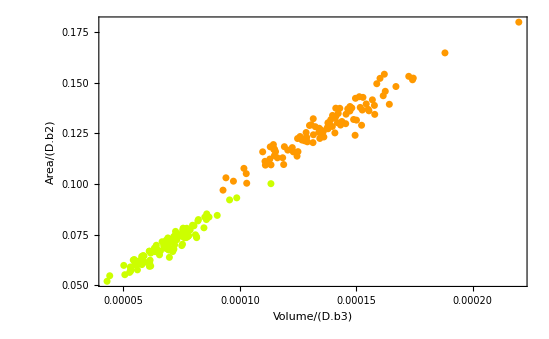

```mathematica
Show[PlotGeral[60,2,5,100,0.1],PlotGeral[30,2,5,100,0.2],PlotRange-> All]
```

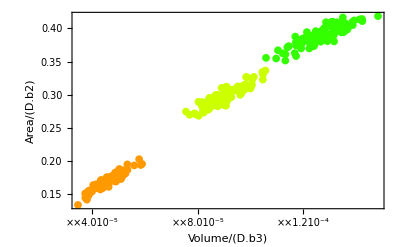

```mathematica
Show[PlotGeral[100,3,9,100,0.1],PlotGeral[200,3,9,100,0.2],PlotGeral[300,3,9,100,0.3],PlotRange->All]
```

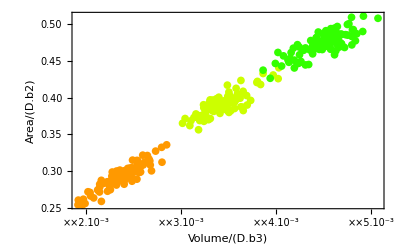

```mathematica
Show[PlotGeral[200,1,3,100,0.1],PlotGeral[300,1,3,100,0.2],PlotGeral[400,1,3,100,0.3],PlotRange->All]
```

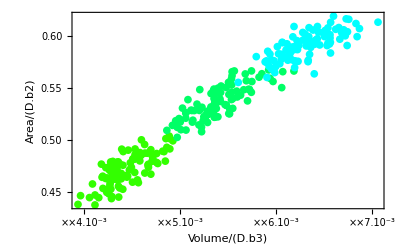

```mathematica
Show[PlotGeral[400,1,3,100,0.3],PlotGeral[500,1,3,100,0.4],PlotGeral[600,1,3,100,0.5],PlotRange->All]
```

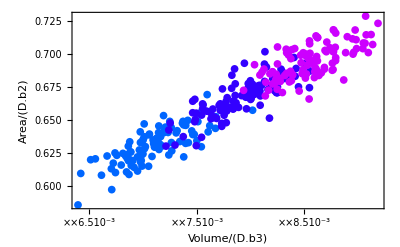

```mathematica
Show[PlotGeral[700,1,3,100,0.6],PlotGeral[800,1,3,100,0.7],PlotGeral[900,1,3,100,0.8],PlotRange->All]
```